```mathematica
Cos[ArcTan[Pi/2]]
```

1/(√(1+π^2/4))

```mathematica
Sin[ArcTan[Pi/2]]
```

π/(2 √(1+π^2/4))

```mathematica
phi=Pi/4
```

π/4

```mathematica
(*Решаем систему*)sol=DSolve[{f'[x]Cos[θ[x]]-f[x]θ'[x]Sin[θ[x]]==Log[f[x]]Cos[ϕ]+θ[x]Sin[ϕ], f'[x]Sin[θ[x]]+f[x]θ'[x]Cos[θ[x]]==-Log[f[x]]Sin[ϕ]+θ[x]Cos[ϕ], f[0]==1,θ[0]==Pi/4},{f[x],θ[x]},x];

(*Извлекаем f(x)*)
fSol=f[x]/. First[sol];
sSol=θ[x]/.sol[[2]];

(*Строим график для конкретных констант*)
Plot[fSol/. {C[1]->0,C[2]->1},{x,-1,1},PlotLabel->"График f(x)",AxesLabel->{"x","f(x)"},PlotRange->All]
```

ReplaceAll::reps: {Cos[θ[x]] f'[x]-f[x] Sin[θ[x]] θ'[x]==Cos[ϕ] Log[f[x]]+Sin[ϕ] θ[x],Sin[θ[x]] f'[x]+Cos[θ[x]] f[x] θ'[x]==-Log[f[x]] Sin[ϕ]+Cos[ϕ] θ[x],f[0]==1,θ[0]==π/4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {f[x],θ[x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Cos[θ[-0.999959]] f'[-0.999959]-1. f[-0.999959] Sin[θ[-0.999959]] θ'[-0.999959]==Cos[ϕ] Log[f[-0.999959]]+Sin[ϕ] θ[-0.999959],«1»==«1»,«1»,θ[0.]==0.785398} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
sol=NDSolve[{f'[x]Cos[θ[x]]-f[x]*θ'[x]Sin[θ[x]]==Log[f[x]]Cos[ϕ]+θ[x]Sin[ϕ], f'[x]Sin[θ[x]]+f[x]*θ'[x]Cos[θ[x]]==-Log[f[x]]Sin[ϕ]+θ[x]Cos[ϕ],f[0]==1,(*Начальное условие для f(x)*)θ[0]==Pi/4                  (*Начальное условие для θ(x)*)},{f,θ},{x,0.1,1}];(*Диапазон по x*)(*Вычисляем вещественную часть*)realPart[x_]:=Re[f[x] Exp[I θ[x]]/. {sol[[1]], sol[[2]]}];
(*Строим график вещественной части*)Plot[realPart[x],{x,0.1,1},PlotLabel->"Вещественная часть Re[f(x)exp(iθ(x))]",AxesLabel->{"x","Re[f(x)exp(iθ(x))]"},PlotStyle->Thick,PlotRange->All]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

NDSolve::dsvar: 0.100018 cannot be used as a variable.

ReplaceAll::reps: {Cos[θ[0.100018]] f'[0.100018]-f[0.100018] Sin[θ[0.100018]] θ'[0.100018]==Cos[ϕ] Log[f[0.100018]]+Sin[ϕ] θ[0.100018],Sin[θ[«20»]] f'[«20»]+«1»==«1»,«1»,θ[0]==π/4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {f,θ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Cos[θ[0.100018]] f'[0.100018]-1. f[0.100018] Sin[θ[0.100018]] θ'[0.100018]==Cos[ϕ] Log[f[0.100018]]+Sin[ϕ] θ[0.100018],«1»==«1»,«1»,θ[0.]==0.785398} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.118386 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

-10

100

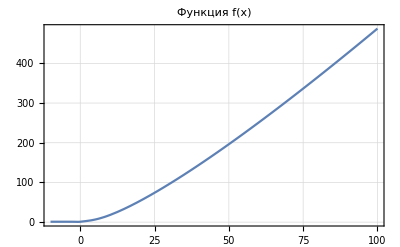

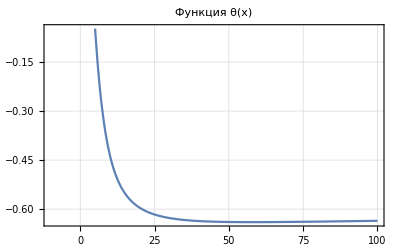

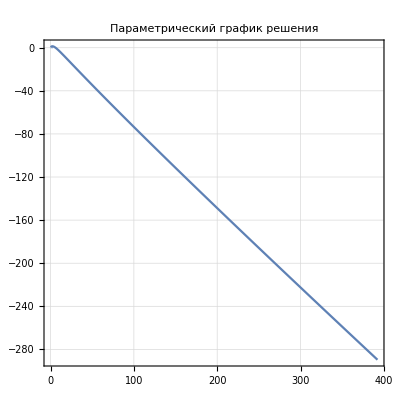

```mathematica
LeftBound=-10
RightBound=100
(*Параметры*)phi=Pi/6;(*Можно изменить на нужное значение угла φ*)(*Система дифференциальных уравнений*)equations={f'[x] Cos[theta[x]]-f[x]*theta'[x] Sin[theta[x]]==Log[f[x]] Cos[phi]+theta[x] Sin[phi],f'[x] Sin[theta[x]]+f[x]*theta'[x] Cos[theta[x]]==-Log[f[x]] Sin[phi]+theta[x] Cos[phi],f[0]==1,theta[0]==Pi/4 (*Добавляем начальное условие для theta,так как система второго порядка*)};

(*Численное решение*)
sol=NDSolve[equations,{f,theta},{x,LeftBound,RightBound}];(*Интервал x от 0 до 5,можно изменить*)(*Построение графиков*)Plot[Evaluate[f[x]/. sol],{x,LeftBound,RightBound},PlotLabel->"Функция f(x)",Frame->True,GridLines->Automatic]
Plot[Evaluate[theta[x]/. sol],{x,LeftBound,RightBound},PlotLabel->"Функция θ(x)",Frame->True,GridLines->Automatic]

(*Параметрический график для визуализации траектории*)
ParametricPlot[Evaluate[{f[x] Cos[theta[x]],f[x] Sin[theta[x]]}/. sol],{x,LeftBound,RightBound},PlotLabel->"Параметрический график решения",Frame->True,GridLines->Automatic,AspectRatio->1]
```

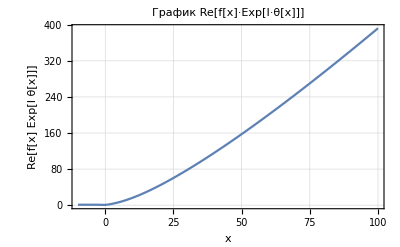

```mathematica
rePart[x_]:=Re[f[x] Exp[I theta[x]]/. sol[[1]]]

(*Построение графика действительной части*)
Plot[rePart[x],{x,LeftBound,RightBound},PlotLabel->"График Re[f[x]·Exp[I·θ[x]]]",Frame->True,GridLines->Automatic,AxesLabel->{"x","Re[f[x] Exp[I θ[x]]]"}]
```